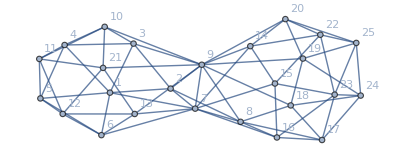

```mathematica
Graph[plantri[[24534]], VertexLabels->"Name"]
```

```mathematica
Graph[plantri[[24534]]]//EdgeList//Length
```

69

```mathematica
ttt=Calc[24534]
```

$Aborted

```mathematica
Clear[Calc]
```

```mathematica
Experiment[Graph[plantri[[24534]]],1<->2]
```

{520,280,240}

```mathematica
Experiment[Graph[plantri[[24534]]],9<->7]
```

{728,280,448}

```mathematica
VerifyHypothesis23[{{520,280,240},{728,280,448}}]
```

{True,True,True,True}

```mathematica
448/280
```

8/5

```mathematica
280/240
```

7/6

```mathematica
FactorList
```

```mathematica
Level
```

```mathematica
f=ChromaticPolynomial[Graph[plantri[[24534]]],x]
```

942985903680 x-6796338423300 x^2+23339731538934 x^3-50975373793776 x^4+79685926802785 x^5-95080738884537 x^6+90133495770582 x^7-69730685552532 x^8+44858357910465 x^9-24316915417767 x^10+11211363509268 x^11-4423745165216 x^12+1499282037542 x^13-437041065269 x^14+109480643951 x^15-23495032315 x^16+4295308694 x^17-663201178 x^18+85410337 x^19-9012942 x^20+759543 x^21-49179 x^22+2298 x^23-69 x^24+x^25

```mathematica
TableForm[Level[f,1]/.x->4//FactorInteger,TableDepth->2]
```

{2,8} | {3,4} | {5,1} | {17,1} | {1061,1} | {2017,1} | 
{-1,1} | {2,6} | {3,3} | {5,2} | {7793,1} | {323003,1} | 
{2,7} | {3,7} | {421,1} | {977,1} | {12973,1} |  | 
{-1,1} | {2,12} | {3,1} | {197,1} | {5390796721,1} |  | 
{2,10} | {5,1} | {19,1} | {113,1} | {541,1} | {13720891,1} | 
{-1,1} | {2,12} | {3,1} | {7,1} | {43,1} | {102197,1} | {1030307,1}
{2,15} | {3,2} | {11,1} | {17,1} | {26777627977,1} |  | 
{-1,1} | {2,18} | {3,1} | {349,1} | {16650115939,1} |  | 
{2,18} | {3,1} | {5,1} | {11,2} | {61,1} | {2347,1} | {172633,1}
{-1,1} | {2,20} | {3,2} | {7,1} | {128461,1} | {3004669,1} | 
{2,24} | {3,1} | {13,1} | {4649,1} | {15458747,1} |  | 
{-1,1} | {2,29} | {13,1} | {233,1} | {643,1} | {70979,1} | 
{2,27} | {283489,1} | {2644339,1} |  |  |  | 
{-1,1} | {2,28} | {17,2} | {29,1} | {52146649,1} |  | 
{2,30} | {7,1} | {29,1} | {37,1} | {14576041,1} |  | 
{-1,1} | {2,32} | {5,1} | {227,1} | {20700469,1} |  | 
{2,35} | {2147654347,1} |  |  |  |  | 
{-1,1} | {2,37} | {17,1} | {2347,1} | {8311,1} |  | 
{2,38} | {499,1} | {171163,1} |  |  |  | 
{-1,1} | {2,41} | {3,2} | {500719,1} |  |  | 
{2,42} | {3,1} | {17,1} | {53,1} | {281,1} |  | 
{-1,1} | {2,44} | {3,1} | {13,2} | {97,1} |  | 
{2,47} | {3,1} | {383,1} |  |  |  | 
{-1,1} | {2,48} | {3,1} | {23,1} |  |  | 
{2,50} |  |  |  |  |  |